```mathematica
Qdotnpstr=" -4.7410075971227e+16";
Qtsqstr=" 5.69982133597215e+32";
Bsqstr=" 0.000138012109654678";
DDstr=" 1.09936312219231e+15";
Scstr=" 8.56725401024624e+56";
QdotBstr="                    0";
WWpstr="  6.0137256210385e+16";
Qtcon1str="     74749988567538.8";
Qtcon2str="                    0";
Qtcon3str="                    0";
Bcon1str="                    0";
Bcon2str="   0.0122463847458348";
Bcon3str="                    0";
```

```mathematica
$MinPrecision=30
```

30

```mathematica
myprec=30
```

30

```mathematica
str=StringToStream[Qdotnpstr]
Qdotnp=Read[str,Number]
str=StringToStream[Qtsqstr]
Qtsq=Read[str,Number]
str=StringToStream[Bsqstr]
Bsq=Read[str,Number]
str=StringToStream[DDstr]
DD=Read[str,Number]
str=StringToStream[Scstr]
Sc=Read[str,Number]
str=StringToStream[QdotBstr]
QdotB=Read[str,Number]
str=StringToStream[WWpstr]
WWp=Read[str,Number]
S=QdotB
```

InputStream[String,40]

-4.74101×10^16

InputStream[String,41]

5.69982×10^32

InputStream[String,42]

0.000138012

InputStream[String,43]

1.09936×10^15

InputStream[String,44]

8.56725×10^56

InputStream[String,45]

0

InputStream[String,46]

6.01373×10^16

0

```mathematica
(*
DD=31622.776617495183
Qdotnp=-9.999684782233827*^8
Qtsq=1.0000002010000104*^18
Clear[Qdotnp,Qtsq,Bsq,DD,QdotB,S,WWp]
*)
```

```mathematica
(* MUST CHOOSE *)
```

```mathematica
(*GAMMA=4/3*)
GAMMA=2.0
```

2.

```mathematica
W=Wp+DD
X=Bsq+W
X2=X^2
SoW=S/W
utsqtop=Qtsq+(Bsq+2*W)*SoW^2
utsqbottom=(Bsq^2-Qtsq)+2*Bsq*W+W^2-SoW^2*(Bsq+2*W)
utsq=utsqtop/utsqbottom
(*Clear[utsq]*)
gammasq=1+utsq
gamma=Sqrt[gammasq]
vsq=1-1/gammasq
wmrho0=(Wp-DD*utsq/(1+gamma))/gammasq
GAMMAM1=GAMMA-1
IGAMMAR=GAMMAM1/GAMMA
p=IGAMMAR*wmrho0
p=1.31885760048493``20*10^16 (* fixed if known *)
(* cold grmhd *)
(*p=0 *)
rho0=DD/gamma
Ss=Log[((wmrho0 (-1+GAMMA))/GAMMA)^(1/(-1+GAMMA)) rho0^(-1-1/(-1+GAMMA))]
resid=X2(Qdotnp+Wp-p+Bsq/2)+1/2(Bsq*Qtsq-QdotB^2)
oldresid=(Qdotnp+Wp-p+Bsq/2)+1/2(Bsq*Qtsq-QdotB^2)/X2
entropyresid=-Sc*1.05+DD*Ss
newentropyresid=Wp*(-Sc*1.05+DD*Ss)
```

1.09936×10^15+Wp

1.09936×10^15+Wp

(1.09936×10^15+Wp)^2

0

5.69982×10^32

-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2

(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)

1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)

√(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))

1-1/(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))

(Wp-6.26617×10^47/((-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2) (1+√(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))))/(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))

1.

0.5

(0.5 (Wp-6.26617×10^47/((-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2) (1+√(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))))))/(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))

1.31885760048493×10^16

(1.09936×10^15)/(√(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))

Log[4.13702×10^-31 (1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))^1. ((Wp-6.26617×10^47/((-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2) (1+√(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))))/(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))^1.]

3.93322×10^28+(-6.05987×10^16+Wp) (1.09936×10^15+Wp)^2

-6.05987×10^16+Wp+(3.93322×10^28)/((1.09936×10^15+Wp)^2)

-8.99562×10^56+1.09936×10^15 Log[4.13702×10^-31 (1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))^1. ((Wp-6.26617×10^47/((-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2) (1+√(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))))/(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))^1.]

Wp (-8.99562×10^56+1.09936×10^15 Log[4.13702×10^-31 (1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2))^1. ((Wp-6.26617×10^47/((-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2) (1+√(1+5.69982×10^32/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))))/(1+(5.69982×10^32)/(-5.69982×10^32+0.000276024 (1.09936×10^15+Wp)+(1.09936×10^15+Wp)^2)))^1.])

```mathematica
(* Now find solution *)
```

```mathematica
sols=NSolve[oldresid==0,Wp]
```

SetPrecision::precsm: Requested precision 20.9409 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision will be suppressed during this calculation.

{{Wp→6.05987×10^16},{Wp→-1.09936×10^15},{Wp→-1.09936×10^15}}

```mathematica
myWp=sols[[1,1,2]]
```

6.05987×10^16

```mathematica
sols=FindRoot[oldresid==0,{Wp,8*10^8}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{Wp→8.×10^8}

```mathematica
myWp=sols[[1,2]]
```

1.37092×10^9

```mathematica
Plot[oldresid,{Wp,0,10^(10)},PlotRange->{-DD/10,DD},PlotPoints->1000]
```

-Graphics-

```mathematica
myWp=sols[[3,1,2]]
```

Part::partw: Part 3 of {Wp → 8.000000000000024`*^8} does not exist.

{Wp→8.×10^8}⟦3,1,2⟧

```mathematica
(*sols=Solve[resid==0,Wp]*)
sols=NSolve[entropyresid==0,Wp]
sols=NSolve[newentropyresid==0,Wp]
(*sols=NSolve[resid==0,Wp,WorkingPrecision->50, PrecisionGoal->25]*)
(*sols=NSolve[resid==0,Wp]*)
solWp=sols[[1,1,2]]
```

{{Wp→2.97278×10^-8}}

Solve::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[0.0000109794+9.8241×10^-7 Log[(1.67745×10^22 (Wp-2.70401×10^-20/((-2.75243×10^-14+(9.8241×10^-7+Wp)^2) (1+√(1+(2.75243×10^-14)/(-2.75243×10^-14+(9.8241×10^-7+Wp)^2)))))^3)/(1+(2.75243×10^-14)/(-2.75243×10^-14+(9.8241×10^-7+Wp)^2))]==0,Wp]

Solve::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[Wp (0.0000109794+9.8241×10^-7 Log[(1.67745×10^22 (Wp-2.70401×10^-20/((-2.75243×10^-14+(9.8241×10^-7+Wp)^2) (1+√(1+(2.75243×10^-14)/(-2.75243×10^-14+(9.8241×10^-7+Wp)^2)))))^3)/(1+(2.75243×10^-14)/(-2.75243×10^-14+(9.8241×10^-7+Wp)^2))])==0,Wp]

0.0000109794+9.8241×10^-7 Log[(1.67745×10^22 (Wp-2.70401×10^-20/((-2.75243×10^-14+(9.8241×10^-7+Wp)^2) (1+√(1+(2.75243×10^-14)/(-2.75243×10^-14+(9.8241×10^-7+Wp)^2)))))^3)/(1+(2.75243×10^-14)/(-2.75243×10^-14+(9.8241×10^-7+Wp)^2))]

```mathematica
(* utsq and chi as functions of W' *)
```

```mathematica
sols=FindRoot[oldresid==0,{Wp,DD}]
```

{Wp→4.79273×10^9}

```mathematica
sols=FindRoot[entropyresid==0,{Wp,10*10^(-9)}]
sols=FindRoot[newentropyresid==0,{Wp,10*10^(-9)}]
```

{Wp→1.34488×10^-8+7.9879×10^-10 ⅈ}

{Wp→1.03245×10^-8+1.69704×10^-9 ⅈ}

```mathematica
WWp
```

-3.99531×10^-8

```mathematica
DD*Ss//.{Wp->WWp}
DD*Ss//.sols[[1]]
```

1.45532×10^-6+1.61965×10^-6 ⅈ

-4.87896×10^-6

```mathematica
Wp
```

Wp

```mathematica
myWp=1.1876164633823*10^(-09)
myWp=2.15633570149049*10^(-08)
mySs=Ss//.{Wp->myWp}
(D[Ss,Wp]//.{Wp->myWp})
```

1.18762×10^-9

2.15634×10^-8

0.496297

1.54546×10^8

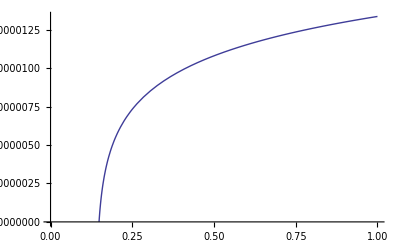

```mathematica
Plot[entropyresid,{Wp,0,10^(-7)}]
```

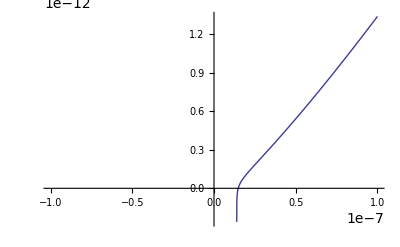

```mathematica
Plot[newentropyresid,{Wp,-10^(-7),10^(-7)}]
```

```mathematica
newentropyresid//.{Wp->2.48*10^(-8)}
```

1.80276×10^-13

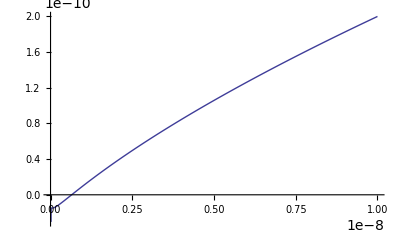

```mathematica
Plot[Wp^(1/2)*entropyresid,{Wp,0,10^(-8)}]
```

```mathematica
Series[entropyresid,{Wp,WWp,1}]
```

2.32934×10^-21+1145.52 (Wp-6.45974×10^-10)+O[Wp-6.45974×10^-10]^2

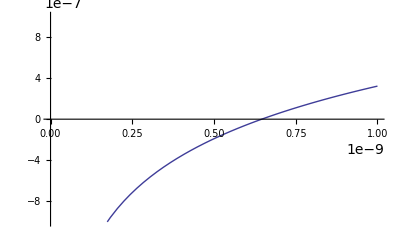

```mathematica
Plot[entropyresid,{Wp,0,10^(-9)},PlotRange->{-10^(-6),10^(-6)}]
```

```mathematica
oldresid//.{Wp->3.53*10^(-7)}
```

0.00109618

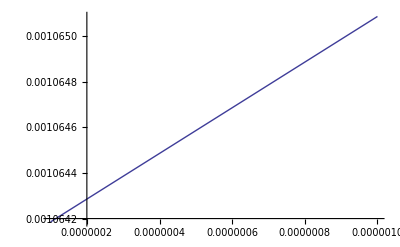

{}

```mathematica
Plot[oldresid,{Wp,10^(-7),10^(-6)}]
```

```mathematica
solWp=WWp
```

1.31868×10^9

```mathematica
solWp=myWp
```

6.05987×10^16

```mathematica
solWp=sols[[1,1,2]]
```

1.28088×10^8

```mathematica
solWp=6.0137256210385*10^(16)
```

6.01373×10^16

```mathematica
finalutsq=Qtsq/(-Qtsq+W^2)//.{Wp->solWp}
gammafinal=Sqrt[1+finalutsq]
finalchi=(Sqrt[Qtsq*(1+finalutsq)/finalutsq]-DD*gammafinal)/gammafinal^2
pressurefinal=(GAMMA-1)/GAMMA*finalchi
pressurefinal=p
ufinal=finalchi-pressurefinal
rhofinal=DD/gammafinal
```

0.176102

1.08448

5.1446×10^16

2.5723×10^16

1.31885760048493×10^16

3.82575×10^16

1.01372×10^15

```mathematica
gcon00=-1.36152449107036``20
alpha=1/Sqrt[-gcon00]
```

-1.36152449107036

0.85701272632976592931584214938

```mathematica
uu0=gammafinal/alpha
uu1=0.00128342432733402
gcov00=-0.734357977191376
gcov01=3.39268187803164
ud0=gcov00*uu0+gcov01*uu1
```

1.26542

0.00128342

-0.734358

3.39268

-0.924918

```mathematica
Tud00=rhofinal*uu0*(1+ud0)+finalchi*uu0*ud0+pressurefinal
```

-4.69281×10^16

```mathematica
Tud00=1*(-rhofinal*gammafinal*(gammafinal-1)-(finalchi)*gammafinal^2+pressurefinal)
```

-4.69487×10^16

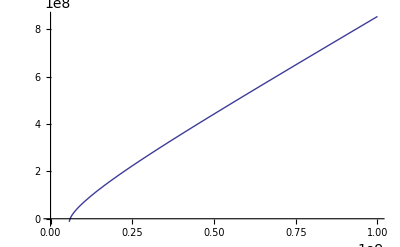

```mathematica
Plot[oldresid,{Wp,0,10^9}]
```

```mathematica
oldresid
```

-1.28088×10^8+Wp

```mathematica
D[oldresid,Wp]//.{Wp->DD}
```

0.75

```mathematica
pressurefinal/(rhofinal*gammafinal^2)
```

0.000654682

```mathematica
minresid=oldresid//.{utsq->0}
```

-8.44827×10^-10+Wp

-1.62697×10^-6

```mathematica
Solve[oldresid==0,Wp]
```

Solve::verif: Potential solution {Wp → -6.20453919729788847337476909161×10^9} (possibly discarded by verifier) should be checked by hand. May require use of limits. More…

{}

```mathematica
oldresid//.{Wp->100.03640347219}
```

60.0218

```mathematica
D[oldresid,Wp]//.{Wp->100.03640347219}
```

0.6

```mathematica
CForm[2.646597331108350460093260788248845493067850910245852952830409295332252674807771304518217488619250907604016522886941361214836540652749633362424765`130.56049976967418*^10]
```

2.646597331108350460093260788248845493067850910245852952830409295332252674807771304518217488619250907604016522886941361214836540\
   6527e10

```mathematica
myWp={Wp->9.67914240676850597055666678996491907098817906960653854319178971088107248360356877164990833496358947020656856316736882294076512797414045940851209`134.17562555401156*^9}
```

{Wp→9.6791424067685059705566667899649190709881790696065385431917897108810724836035687716499083349635894702065685631673688229407651279741405×10^9}

```mathematica
myresid=resid//.myWp
myjac=D[resid,Wp]//.myWp
mydWp=-myresid/myjac
newWp=(Wp//.myWp) + mydWp
mydWp/(Wp//.myWp)
```

1.10068×10^35

6.2651×10^23

-1.75684×10^11

3.74516×10^11

-0.319309

```mathematica
myresid=oldresid//.myWp
myjac=D[oldresid,Wp]//.myWp
mydWp=-myresid/myjac
newWp=(Wp//.myWp) + mydWp
```

3.63595×10^11

0.747919

-4.86142×10^11

6.40573×10^10

```mathematica
myresid=(oldresid/Wp)//.myWp
myjac=D[oldresid/Wp,Wp]//.myWp
mydWp=-myresid/myjac
newWp=(Wp//.myWp) + mydWp
```

0.660842

1.58264×10^-13

-4.17557×10^12

-3.62537×10^12

5.21577×10^23

General::spell1: Possible spelling error: new symbol name "mydWp" is similar to existing symbol "myWp". More…

-1.60258×10^11

```mathematica
504005713285.998
```

5.04006×10^11

```mathematica
Plot[oldresid,{Wp,10^(-23),10^(-16)}]
```

⁃Graphics⁃

```mathematica
dEdW=D[oldresid,Wp]//.{Wp->WWp}
myresid=(oldresid//.{Wp->WWp})
mydW = myresid/dEdW
errW = mydW/Wp //.{Wp->WWp}
```

0.75

6.59742×10^-17

8.79656×10^-17

0.999995

```mathematica
Plot[oldresid,{Wp,.5*10^(10),5*10^(11)}]
```

⁃Graphics⁃

```mathematica
Plot[oldresid/Wp,{Wp,.5*10^(10),5*10^(11)}]
```

⁃Graphics⁃

```mathematica
Plot[resid,{Wp,.5*10^(10),6*10^(11)}]
```

⁃Graphics⁃

```mathematica
myutsq=utsq//.{Wp->10^x}
Plot[myutsq,{x,9,12}]
```

(2.52004×10^21)/(-2.52004×10^21+(223607.+10^x)^2)

⁃Graphics⁃

```mathematica
Solve[utsqbottom==0,Wp]
```

{{Wp→-5.02002×10^10},{Wp→5.01998×10^10}}

```mathematica
utsq//.{Wp->5*10^12}
```

0.000100812

```mathematica
Table[sols[[i,1,2]]-WWp,{i,1,3}]
```

{-2.40544×10^10,-3.33729×10^10+12202.69431597171410735642758319730504296598385226970625638720395919753586988797516572232204613078309332342239083381168649620562278 ⅈ,-3.33729×10^10-12202.69431597171410735642758319730504296598385226970625638720395919753586988797516572232204613078309332342239083381168649620562278 ⅈ}

```mathematica
myWp=128633404.169091
Table[sols[[i,1,2]]-myWp,{i,1,3}]
Table[(sols[[i,1,2]]-myWp)/myWp,{i,1,3}]
```

1.28633×10^8

{1.66045×10^10-105409. ⅈ,1.66045×10^10+105409. ⅈ,5.00711×10^10}

{129.084-0.000819455 ⅈ,129.084+0.000819455 ⅈ,389.255}

```mathematica
oldresid//.{Wp->5*10^(10)}
```

-9.96866×10^7-5002.13 ⅈ

```mathematica
resid//.{Wp->5*10^(9)}
```

1.98884×10^30-1.39622×10^25 ⅈ

```mathematica
Plot[resid,{Wp,1*10^8,5*10^(10)}]
```

Plot::plnr: resid is not a machine-size real number at Wp = 1.00002×10^8. More…

Plot::plnr: resid is not a machine-size real number at Wp = 2.12429×10^9. More…

Plot::plnr: resid is not a machine-size real number at Wp = 4.33196×10^9. More…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. More…

⁃Graphics⁃

```mathematica
god1=Qtsq/(-DD+√(DD^2+Qtsq))
god2=-Qtsq/(-DD-√(DD^2+Qtsq))
```

5.02002×10^10

5.01998×10^10

```mathematica
Solve[utsqbottom==0,Wp]
```

{{Wp→-5.02002×10^10},{Wp→5.01998×10^10}}

```mathematica
DD
```

279508.

```mathematica
5.01997722396452*^10-5.01997722391432*^10
```

0.501999